```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[FontSize->20,FontFamily->"Linux Libertine Display"]];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
(* if rot is modified, conum should be modified in consequence *)
rot=0; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

idos(p,q)=pF_(n-1)+qF_n

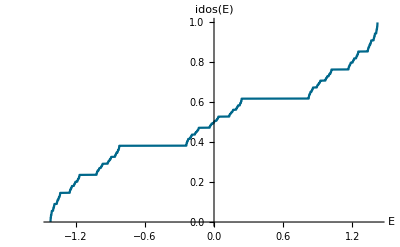

```mathematica
ρ=0.5;
n=17;
ham=hp[n-2,ρ,1.];
{val,vec}=Eigensystem[ham];
ord=Ordering[val];
vec=vec[[ord]];
val=val[[ord]];
(* translate and scale spectrum btw 0 and 1 *)
(*val=(val-val[[1]])/(val[[-1]]-val[[1]]);*)
idos=Table[{val[[i]],i/Fibonacci[n]},{i,Fibonacci[n]}];
(* p = -1, q = 1 *)
p1={val[[#]],#}&[Fibonacci[n-2]+1];
(* p = 1, q = 0*)
p2={val[[#]],#}&[Fibonacci[n-1]];
ListPlot[idos,Joined->True,PlotRange->All,PlotStyle->{BostonBlue}, AxesStyle->Directive[FontSize->15,FontFamily->"Linux Libertine Display"],AxesLabel->st/@{"E","idos(E)"}]
```

```mathematica
Export[NotebookDirectory[]<>"idos1.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/idos1.pdf

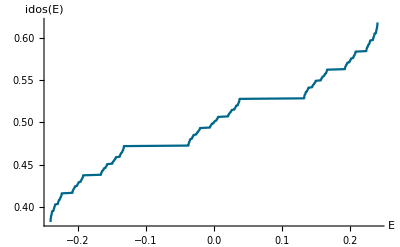

```mathematica
(* p = 4, q = -2 *)
lab1=4Fibonacci[n-1]-2Fibonacci[n]+1;
p1={val[[#]],#}&[lab1];
(* p = -4, q = 3 *)
lab2=-4Fibonacci[n-1]+3Fibonacci[n];
p2={val[[#]],#}&[lab2];
ListPlot[idos[[Fibonacci[n-2]+1;;Fibonacci[n-1]]],Joined->True,PlotRange->All,PlotStyle->{BostonBlue}, AxesStyle->Directive[FontSize->15,FontFamily->"Linux Libertine Display"],AxesLabel->st/@{"E","idos(E)"}]
```

```mathematica
Export[NotebookDirectory[]<>"idos2.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/idos2.pdf

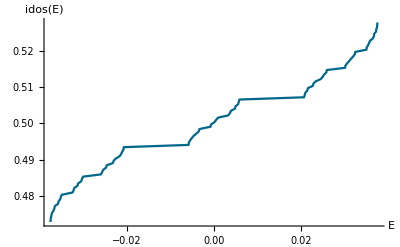

```mathematica
ListPlot[idos[[lab1;;lab2]],Joined->True,PlotRange->All,PlotStyle->{BostonBlue}, AxesStyle->Directive[FontSize->15,FontFamily->"Linux Libertine Display"],AxesLabel->st/@{"E","idos(E)"}]
```

```mathematica
Export[NotebookDirectory[]<>"idos3.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/idos3.pdf

ldos ρ_ii(E)

```mathematica
(* artificial width of the peaks *)
ϵ=3.6/Fibonacci[n];
(* small scale *)
δ=0.01;
Clear[e];
ldos=Apply[Plus,ϵ/((val-e)^2+ϵ^2)];
```

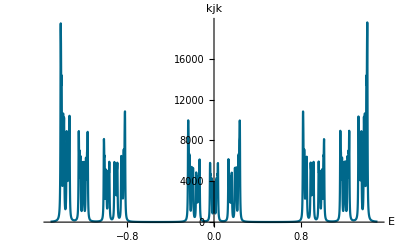

```mathematica
Plot[ldos,{e,-1.5-δ,1.5+δ},PlotRange->All,Axes->{True,False},PlotStyle->{BostonBlue}, AxesStyle->Directive[Large,FontFamily->"Linux Libertine Display"],AxesLabel->{st["E"],"kjk"}]
```

```mathematica
Export[NotebookDirectory[]<>"ldos1.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/ldos1.pdf

```mathematica
(* p = -1, q = 1 *)
p1={val[[#]],#}&[Fibonacci[n-2]+1];
(* p = 1, q = 0*)
p2={val[[#]],#}&[Fibonacci[n-1]];
(* scaling factor on the energy axis *)
s2=(p2-p1)[[1]];
(* artificial width of the peaks *)
ϵ2=s2 ϵ;
Clear[e];
ldos2=Apply[Plus,ϵ2/((val[[Fibonacci[n-2]+1;;Fibonacci[n-1]]]-e)^2+ϵ2^2)];
```

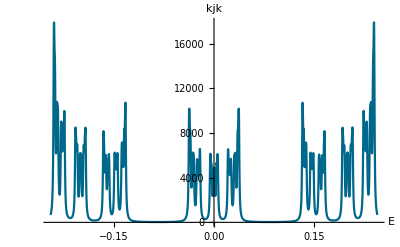

```mathematica
Plot[ldos2,{e,p1[[1]]-δ s2,p2[[1]]+δ s2},PlotRange->All,Axes->{True,False},Axes->{True,False},PlotStyle->{BostonBlue}, AxesStyle->Directive[Large,FontFamily->"Linux Libertine Display"],AxesLabel->{st["E"],"kjk"}]
```

```mathematica
Export[NotebookDirectory[]<>"ldos2.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/ldos2.pdf

```mathematica
(* p = 4, q = -2 *)
lab1=4Fibonacci[n-1]-2Fibonacci[n]+1;
p1={val[[#]],#}&[lab1];
(* p = -4, q = 3 *)
lab2=-4Fibonacci[n-1]+3Fibonacci[n];
p2={val[[#]],#}&[lab2];
(* scaling factor on the energy axis *)
s3=(p2-p1)[[1]];
(* artificial width of the peaks *)
ϵ3=s3 ϵ;
Clear[e];
ldos3=Apply[Plus,ϵ3/((val[[lab1;;lab2]]-e)^2+ϵ3^2)];
```

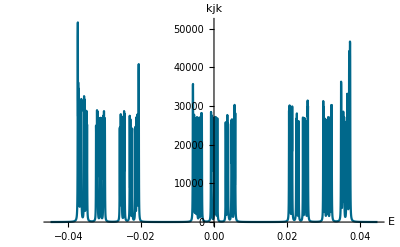

```mathematica
Plot[ldos3,{e,p1[[1]]-δ s3,p2[[1]]+δ s3},PlotRange->All,Axes->{True,False},Axes->{True,False},PlotStyle->{BostonBlue}, AxesStyle->Directive[Large,FontFamily->"Linux Libertine Display"],AxesLabel->{st["E"],"kjk"}]
```

```mathematica
Export[NotebookDirectory[]<>"ldos3.pdf",%]
```

/home/nicolas/git/talks/Oléron 2016/img/ldos3.pdf